```mathematica
AnimateAutomata[rule_, init_,steps_, mapPlot_:ArrayPlot]:=
Module[
{automataHistory=CellularAutomaton[rule,init,steps]},
Animate[
mapPlot@automataHistory[[n]],
{n, 1, steps+1, 1},
AnimationRunning->False,
AnimationRepetitions->Infinity
]
]
```

```mathematica
AnimateAutomata[170, ReplacePart[ConstantArray[0, 11],1->1], 100,ArrayPlot@*List]
```

```mathematica
AnimateAutomata[30, ReplacePart[ConstantArray[0, 11],1->1], 100,ArrayPlot@*List]
```

```mathematica
AnimateAutomata[
<|
"GrowthDecayCases"->{{1,3},{3,4}},
"Neighborhood"->"VonNeumann"
|>,
{{{1}},0},70]
```

```mathematica
AnimateAutomata[{14,{2,1},{1,1,1}},{{{{1}}},0},20, ArrayMesh]
```

```mathematica
AnimateAutomata[<|"TotalisticCode"->14,"Dimension"->3,"Neighborhood"->27|>,{{{{1}}},0},20, ArrayMesh]
```

```mathematica
AnimateAutomata[<|"TotalisticCode"->14,"Dimension"->3,"Neighborhood"->27|>,Table[If[i==j==k||i==21-k==j||i==21-j==k||21-i==j==k, 1, 0],{i, 21}, {j, 21},{k, 21}],100, ArrayMesh]
```

```mathematica
size = 21;
mid = size/2//Ceiling;
sphere=Table[If[(i-mid)^2+(j-mid)^2+(k-mid)^2== Floor[size/2],1, 0],{i, size}, {j, size},{k, size}];
cross=Table[If[i==mid||j==mid||k==mid,1, 0],{i, size}, {j, size},{k, size}];
```

```mathematica
AnimateAutomata[<|"TotalisticCode"->174762,"Dimension"->3,"Neighborhood"->27|>,cross,100, ArrayMesh]
```

```mathematica
AnimateAutomata[<|"TotalisticCode"->349525,"Dimension"->3,"Neighborhood"->27|>,cross,100, ArrayMesh]
```

```mathematica
FromDigits[{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1}, 2]
```

349525

```mathematica
(* GAME OF LIFE EXAMPLES *)
GoLRule={224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}};

block={{1, 1},{1, 1}};
beehive={{0,1,1,0},{1,0,0,1},{0,1,1,0}};
loaf={{0, 1, 1,0},{1, 0, 0, 1},{0, 1, 0, 1},{0, 0, 1, 0}};
boat={{1, 1, 0},{1, 0, 1},{0, 1, 0}};
tub={{0, 1, 0},{1, 0, 1},{0, 1, 0}};

glider={{0,1,0},{0,0,1},{1,1,1}};
spaceship={{1, 0, 0, 1, 0},{0, 0, 0, 0, 1},{1, 0, 0, 0, 1},{0, 1, 1, 1,1}};

blinker={{0,0,0},{1,1,1},{0,0,0}};
toad={{0, 1, 1, 1},{1, 1, 1, 0}};
beacon={{1, 1, 0, 0},{1, 1, 0, 0},{0, 0,1, 1},{0, 0, 1, 1}};
pulsar={
{0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0},{0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0},{0, 0, 0, 0, 1, 1, 0, 0, 0, 1, 1, 0, 0, 0, 0},{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0},{1, 1, 1, 0, 0, 1, 1, 0, 1, 1, 0, 0, 1, 1, 1},{0, 0, 1, 0, 1, 0, 1, 0, 1, 0, 1, 0, 1, 0, 0},{0, 0, 0, 0, 1, 1, 0, 0, 0, 1, 1, 0, 0, 0, 0},{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0},{0, 0, 0, 0, 1, 1, 0, 0, 0, 1, 1, 0, 0, 0, 0},{0, 0, 1, 0, 1, 0, 1, 0, 1, 0, 1, 0, 1, 0, 0},{1, 1, 1, 0, 0, 1, 1, 0, 1, 1, 0, 0, 1, 1, 1},{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0},{0, 0, 0, 0, 1, 1, 0, 0, 0, 1, 1, 0, 0, 0, 0},{0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0},{0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0}};
pentadecathlon={{1, 1, 1},{1, 0, 1},{1, 1, 1},{1, 1, 1},{1, 1, 1},{1, 1, 1},{1, 0, 1},{1, 1, 1}};

gosperGliderRun={
{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0},{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0},{0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0},{0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 1, 0, 0, 0, 1, 1},{0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 1, 1},{1, 1, 0, 0, 1, 1, 0, 0, 0, 0, 1, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0},{1, 1, 0, 0, 1, 1, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0},{0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0},{0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}};

AnimateAutomata[GoLRule,{#,0},120]&/@{block, beehive, loaf, boat, tub, glider, spaceship, blinker, toad, beacon, pulsar, gosperGliderRun}
```

{,,,,,,,,,,,}

```mathematica
GridPlot[data_]:=
MatrixPlot[
data,
Mesh->All,
Frame->False
]
```

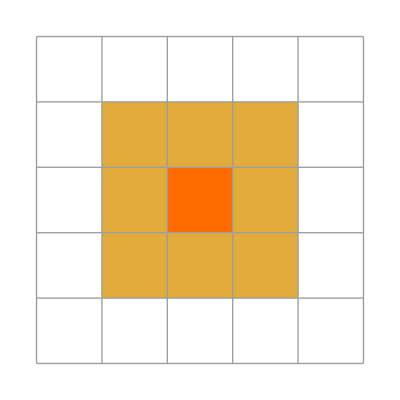

```mathematica
GridPlot@SparseArray[{
{i_,j_}/;i==j==3->2, 
{i_,j_}/;EuclideanDistance[{3, 3}, {i, j}]≤√2->1},
{5,5}
]
```

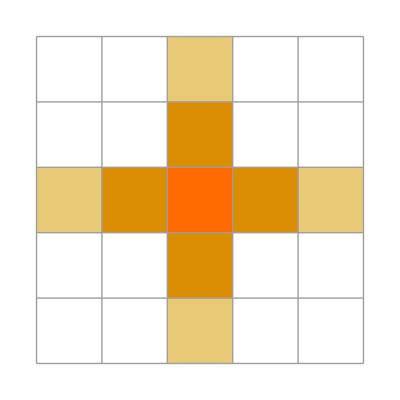

```mathematica
GridPlot@SparseArray[{
{i_,j_}/;i==j==3->3, 
{i_,j_}/;ManhattanDistance[{3, 3},{i,j}]==1->2, 
{i_,j_}/;ManhattanDistance[{3, 3},{i,j}]==2∧EuclideanDistance[{3, 3}, {i, j}]≥√3->1},
{5,5}
]
```

```mathematica
-Graphics-OuterTotalisticCode
```

OuterTotalisticCode -Graphics-

```mathematica
randomInitialState=ReplacePart[ConstantArray[0, 101],51->1];
ImageAssemble@Table[ArrayPlot@CellularAutomaton[(i-1)*16+j-1,randomInitialState, 50 ], {i, 1,16}, {j, 1, 16}]
```

-Graphics-